# Формулы

```mathematica
"Символы"paclet:tutorial/LettersAndLetterLikeForms
```

( = esc)

a → α
b → β
γ → γ
…
f → ϕ    j → φ
e → ϵ  ce → ε
w → ω  o → ω     om → ο

deg  → °

```mathematica
α β ϕ φ
```

α β ϕ φ

```mathematica
"Набор формул"paclet:tutorial/KeyboardShortcutListing#1484044289
```

Ctrl+6 → □^□
Ctrl+2 → √□
…+Ctrl+5 → □^(1/□)
Ctrl+/→ □/□
Ctrl+Space → end subexpression
Alt+/→ (*comment*)

Alt+ ),],}→ (),[],{}
Ctrl+,→  | □ | □ | □
Ctrl+Enter → □
□
□
…→(□ | □ | □
□ | □ | □
□ | □ | □)

# Выражения

Head[a_1, a_2, a_3,…]

```mathematica
"Everything is an Expression"paclet:tutorial/EverythingIsAnExpression
```

Операции:

```mathematica
FullForm[a+b]
```

Plus[a,b]

Функции:

```mathematica
F[x,y]
```

F[x,y]

Типы данных:

```mathematica
PhasePoint[q,p]
```

PhasePoint[q,p]

```mathematica
"Expressions"paclet:tutorial/ExpressionsOverview
```

Head[]
FullForm[]
TreeForm[]

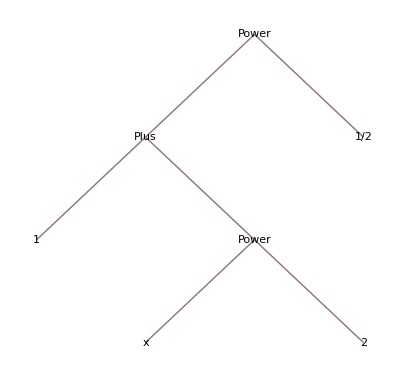

```mathematica
TreeForm[√(1+x^2)]
```

Списки:

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

Part[] (⟦⟧)
Head[] = ⟦0⟧
⟦= [[ 
⟧ = ]]
Range[]
Table[]
Subdivide[]
(для вызова справки выделить имя и нажать F1)

```mathematica
√(1+x^2)⟦1,2,1⟧
```

x

# Правила замены

```mathematica
2+2
```

4

```mathematica
1/2-1/3
```

1/6

```mathematica
2+x
```

2+x

```mathematica
1+x*x
```

1+x^2

Задание правил

Set[]  (=)

```mathematica
x=4;
```

```mathematica
?x
```

Global`x

x=4

```mathematica
1+√x
```

3

Удаление правил, ассоциированных с символом

```mathematica
Clear[x]
```

```mathematica
?x
```

Global`x

```mathematica
x=.
```

Правила с отложенным вычислением

SetDelayed[]  (:=)

```mathematica
x=4;
y=x;
z:=x^2;
```

```mathematica
{x,y,z}
```

{4,4,16}

```mathematica
x=5;
{x,y,z}
```

{5,4,25}

Функция глобальной переменной

```mathematica
x=2;
F[]:=x^2;
F[]
```

4

```mathematica
x=3;
F[]
```

9

Функция с агрументом (паттерн)

```mathematica
F[x_]:=x^2;
F[3]
```

9

Полиморфизм (перегрузка функций)

```mathematica
F[0]:=5;
F[x_]:=x^2;
F[x_,_]:=x^3;
```

```mathematica
?F
```

Global`F

F[]:=x^2
 
F[0]:=5
 
F[x_]:=x^2
 
F[x_,_]:=x^3

```mathematica
{F[0],F[2],F[2,0]}
```

{5,4,8}

```mathematica
F["cat","chaos"]
```

cat^3

```mathematica
F[0]:=0;
F[1]:=1;
F[n_]:=F[n-1]+F[n-2];  (*определение с использованием рекурсии*)
{F[0],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],F[9]}
```

{0,1,1,2,3,5,8,13,21,34}

```mathematica
"Patterns"paclet:tutorial/PatternsOverview
```

"Specifying Types"paclet:tutorial/SpecifyingTypesOfExpressionInPatterns (F[x_type]:=…)
Optional (F[x_:x0]:=…)
PatternTest (F[x_?test]:=…)
Optional with PattenTest (F[x:(_?test):x0]:=…)
Condition (F[x_/;test]:=…)

Sequence of variables (F[x__]:=…)
Parameterized function(F[α_][x_]:=…)
…

# Функциональное программирование

Три эквивалентных способа записи применения функции к единственному аргументу

```mathematica
f@a  (* префиксная запись *)
f[a] (* инфиксная запись *)
a//f (* постфиксная запись *)
```

f[a]

f[a]

f[a]

Композиция функций

```mathematica
A@B@C@X
```

A[B[C[X]]]

### Функции высшего порядка

```mathematica
Apply[f,{1,2,3}] (* применение функции тождественно замене заголовка: List[1,2,3] -> F[1,2,3] *)
```

f[1,2,3]

краткая запись

```mathematica
f@@{1,2,3}
```

f[1,2,3]

```mathematica
ArcTan@@(a+b)
```

ArcTan[a,b]

```mathematica
Plus@@{1,2,a,3,2a}
```

6+3 a

```mathematica
"(порядок применения операторов при преобразовании к полной форме)"paclet:tutorial/OperatorInputForms
```

```mathematica
Map[f,{1,2,3}] (* поэлементное применение функции к списку *)
```

{f[1],f[2],f[3]}

краткая запись

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

Поэлементное применение встроенных функций

```mathematica
1+{1,2,3}
2*{1,2,3}
Sin[{1,2,3}]
```

{2,3,4}

{2,4,6}

{Sin[1],Sin[2],Sin[3]}

Атрибут Listable

```mathematica
Attributes[Plus]
Attributes[Sin]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

{Listable,NumericFunction,Protected}

Сравнение функциональных выражений

```mathematica
f@{1,2,3} (* префиксная запись функции *)
f@@{1,2,3} (* Apply *)
f/@{1,2,3} (* Map *)
```

f[{1,2,3}]

f[1,2,3]

{f[1],f[2],f[3]}

Apply[] (@@)
Map[] (/@)
Nest[]
Fold[]
NestList[]

```mathematica
Nest[f,a,5]
```

f[f[f[f[f[a]]]]]

```mathematica
NestList[f,a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

### Анонимные (безымянные) функции

```mathematica
Function[{x,y,z},y^2+√z]
```

Function[{x,y,z},y^2+√z]

```mathematica
F=Function[{x,y,z},y^2+√z];
F[1,2,3]
```

4+√3

```mathematica
Function[{x,y,z},y^2+√z][1,2,3]
Function[{x,y,z},y^2+√z]@@{1,2,3}
```

4+√3

4+√3

краткая запись через безымянные аргументы

```mathematica
F=(#^2)&
G=(#1^2+√#2)&
```

#1^2&

#1^2+√#2&

```mathematica
(#^2)&@5
```

25

```mathematica
F[5]
```

25

```mathematica
(#2^2+√#3)&@@{1,2,3}
```

4+√3

использование анонимной функции в качестве аргумента функции высшего порядка

```mathematica
SortBy[{1,2,3,4,5,6},N[Sin[#]]&]
```

{5,4,6,3,1,2}

```mathematica
Nest[1+1/#&,⋯,7]
```

1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/⋯))))))

```mathematica
Nest[1+1/#&,⋯,7]//TeXForm
```

\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{\cdots }+1}+1}+1}+1}+1}+1}+1

```mathematica
Nest[1+1/#&,1,15]//N
(1+√5)/2//N
```

1.61803

1.61803

# Бифуркационная диаграмма

Логистическое отображение

```mathematica
Subscript[x, n+1]=k Subscript[x, n] (1-Subscript[x, n])
```

```mathematica
k=3.5;
k # (1-#)&;
```

```mathematica
(*динамика системы*)
NestList[k # (1-#)&,0.1,100]//ListLinePlot
```

```mathematica
(*предельные точки*)
NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧//ListPlot
```

### Финальный код

```mathematica
ListPlot[Table[NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧,{k,0,4,.001}]ᵀ]
```

```mathematica
ListLinePlot[Table[Outer[List,{k},Sort[NestList[k #(1-#)&,.5,10000]⟦-32;;⟧]]⟦1⟧,{k,0,4,.001}]ᵀ,AxesLabel->{"k","x"},LabelStyle->Large,ImageSize->Large]
```